## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

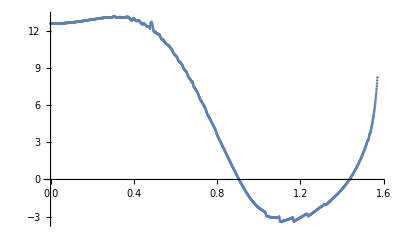

```mathematica
ListPlot[Transpose@{αs,Drs}]
```

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

Maybe Fitting is even better, curves will be smoother. If the data has discontinuities, so does the interpolating curve. Unlike the fitting curve.

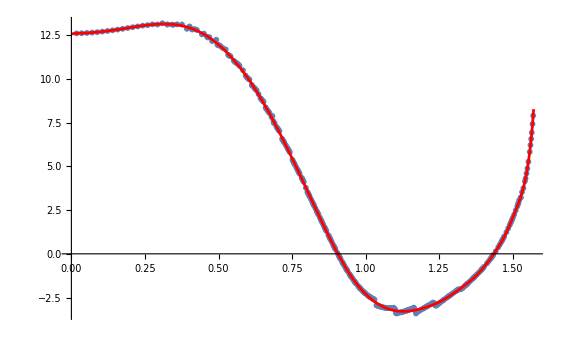

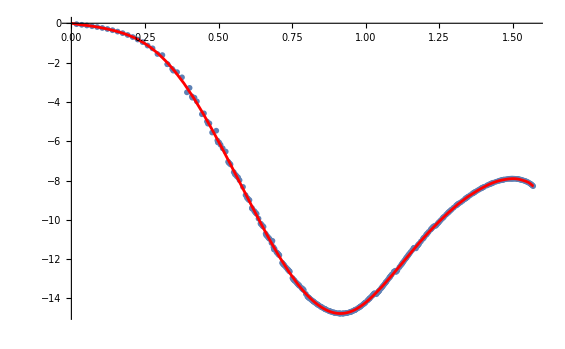

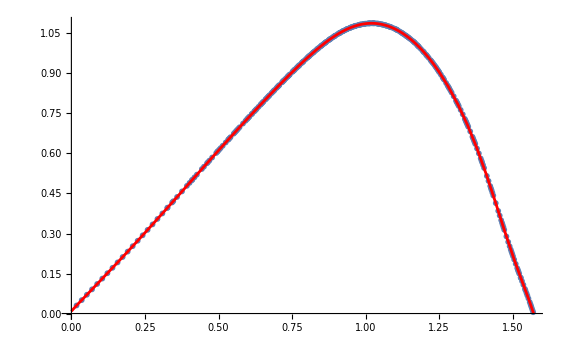

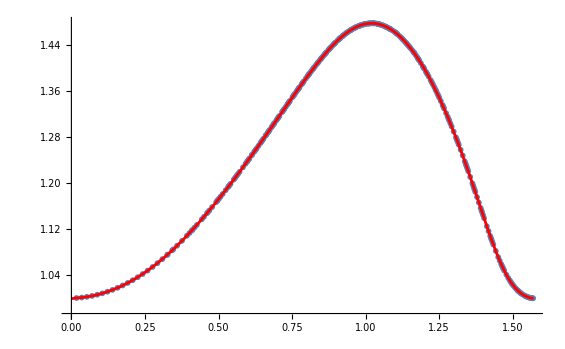

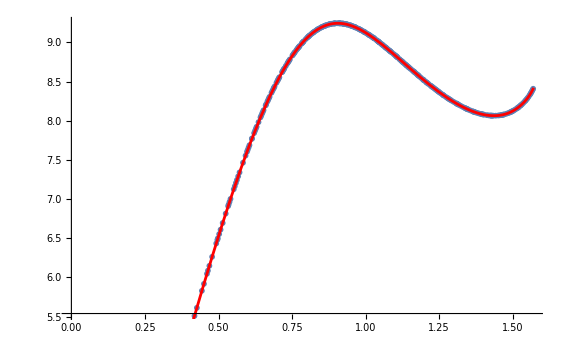

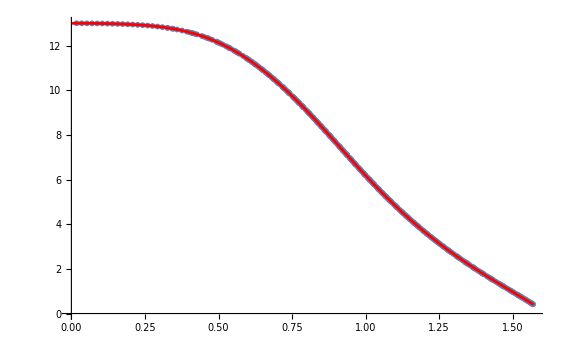

```mathematica
ndegree=55;(*14,25,43,44,55*)
monomials=Table[x^i,{i,0,ndegree}];
ur[α_]=Fit[Transpose@{αs,urs},monomials,x]/.x->α;
uτ[α_]=Fit[Transpose@{αs,uτs},monomials,x]/.x->α;
r[α_]=Fit[Transpose@{αs,rs},monomials,x]/.x->α;
Dr[α_]=Fit[Transpose@{αs,Drs},monomials,x]/.x->α;
τ[α_]=Fit[Transpose@{αs,τs},monomials,x]/.x->α;
Dτ[α_]=Fit[Transpose@{αs,Dτs},monomials,x]/.x->α;
Show[
ListPlot[Transpose@{αs,Drs}],
Plot[Dr[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,Dτs}],
Plot[Dτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,urs}],
Plot[ur[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,uτs}],
Plot[uτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,rs}],
Plot[r[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,τs}],
Plot[τ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV*)
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ϵ=0.001*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
vev=0.09;(*??? vev of sigma field ??? pion decay constant ~92MeV ???, in GeV*)
```

```mathematica
Quiet[
{
(*Why does this not work with "=" instead of ":="*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
     linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];

Nαs=1500;
αs=linspace[0,Pi/2,Nαs];
dαs=(Pi/2)/Nαs;
urs=ur[αs]; (*dimensionless*)
uτs=uτ[αs]; (*dimensionless*)
rs=r[αs];(*in IGeV*)
Drs=Dr[αs];(*in IGeV*)
τs=τ[αs];(*in IGeV*)
Dτs=Dτ[αs];
},
{InterpolatingFunction::dmval}];
```

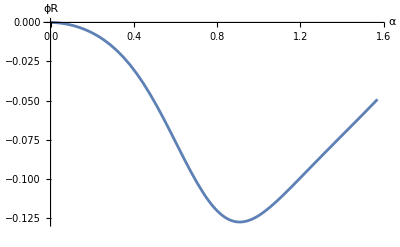

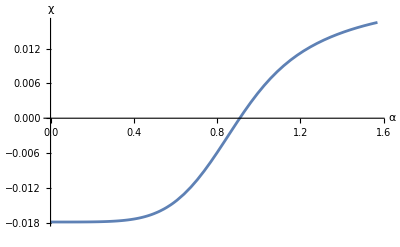

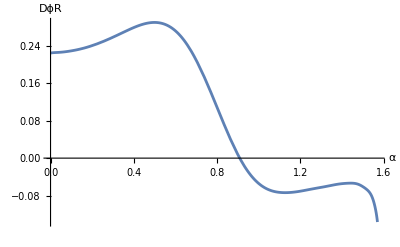

InterpolatingFunction::dmval: Input value {1.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

20240808_144122

/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/data/init_pion/init0.csv

```mathematica
Mass = mπ;

ratio = 0;
sign =- 1;
Epot = ratio*ϵ;
Ekin = (1 - ratio)*ϵ;
ϕRstart = Sqrt[2*Epot]/Mass;
χstart = sign*Sqrt[2*Ekin];

ODEs = {
      ϕR'[α] == χ[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α]),
      χ'[α] == -Mass^2*ϕR[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α])};
ICs = {ϕR[0] == ϕRstart, χ[0] == χstart};
solution = NDSolve[{ODEs, ICs}, {ϕR[α], χ[α]}, {α, 0, Pi/2}];

ϕRfunc[t_] := (ϕR[α] /. solution[[1]] /. α -> t);
χfunc[t_] := (χ[α] /. solution[[1]] /. α -> t);
DϕRfunc[t_] := (-Dr[t]*uτ[t] + Dτ[t]*ur[t])*χfunc[t];

Plot[ϕRfunc[x], {x, 0, Pi/2}, AxesLabel -> {α, ϕR}]
Plot[χfunc[o], {o, 0, Pi/2}, AxesLabel -> {α, χ}]
Plot[DϕRfunc[o], {o, 0, Pi/2}, AxesLabel -> {α, DϕR}]

initdata = Table[{α, Re@ϕRfunc[α], Im@ϕRfunc[α], Re@DϕRfunc[α], Im@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# epsilon:" <> ToString[ϵ] <> "\n# mass:" <> ToString[Mass]}];
timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]]
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_pion/init0.csv"],table,"Table","FieldSeparators"->","]
(*Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_real_"<>timestamp<>"/init10.csv"],table,
"Table","FieldSeparators"->","]*)
```

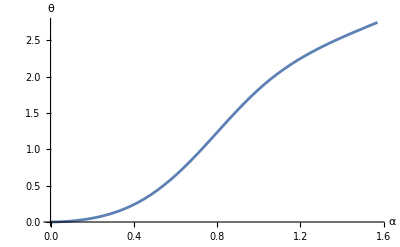

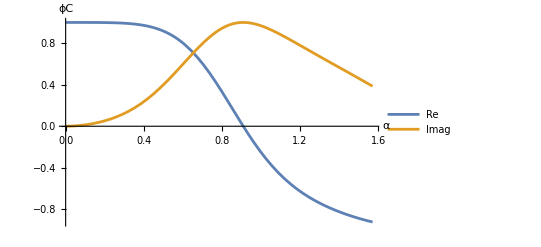

```mathematica
χθ=mπ;
n=1;

ODEs={θ'[α]==χθ*(-Dτ[α]*uτ[α]+Dr[α]*ur[α])};
ICs={θ[0]==0};
solution=NDSolve[{ODEs,ICs},{θ[α]},{α,0,Pi/2}];
θfunc[t_]:=(θ[α]/.solution[[1]]/.α->t);
ϕC[t_]:=Sqrt[n]*Exp[I*θfunc[t]]

Plot[θfunc[x],{x,0,Pi/2},AxesLabel->{α,θ}]
Plot[{Re@ϕC[x],Im@ϕC[x]},{x,0,Pi/2},PlotLegends->{"Re","Imag"},AxesLabel->{α,ϕC}]
```